{{1,6824},{2,1547},{3,352},{4,121},{5,61},{6,26},{7,14},{8,11},{9,8},{10,3},{11,3},{12,1},{13,2},{14,3},{15,1},{21,2},{7623,1}}

{{1,4700},{2,1374},{3,654},{4,323},{5,201},{6,113},{7,78},{8,62},{9,48},{10,28},{11,11},{12,7},{13,4},{14,7},{15,1},{16,4},{17,3},{18,2},{19,3},{20,2},{21,2},{23,2},{24,1},{27,3},{29,1},{30,1},{4991,1}}

9.21171-3.24863 x

8.64218-2.14441 x

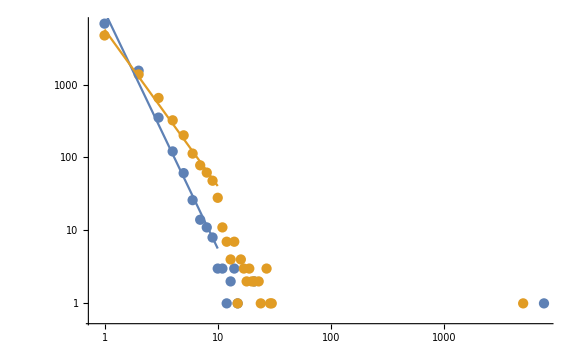

```mathematica
tableEn=Import[NotebookDirectory[]<>"componentsData_en_20k","Table"]//Sort
tableRu=Import[NotebookDirectory[]<>"componentsData_ru_20k","Table"]//Sort
lineEn=Normal@LinearModelFit[Log[tableEn⟦1;;9⟧],{1,x},x]
lineRu=Normal@LinearModelFit[Log[tableRu⟦1;;9⟧],{1,x},x]
Show[ListLogLogPlot[{tableEn,tableRu},ImageSize->Large],Plot[{lineEn,lineRu},{x,0,Log[10]}]]
```